# B → K^* Form Factors Horgan et al. arXiv:1310.3722 - v2 - v3 Horgan et al. arXiv:1501.00367 - v2

```mathematica
Quit[]
```

```mathematica
Needs["MultivariateStatistics`"]
```

# Results from arXiv:1310.3722 v2

## Parametrizations for eq(40) with c_01= 0

```mathematica
MB = 5.279;
MKstar = 0.896;
MBsStar = 5.4154;
MBs1 = MB + 0.550;
tPlus = (MB + MKstar)^2;
t0 = 12;
deltaX = 0;
```

```mathematica
z[t_, t0_, tPlus_] := (Sqrt[tPlus - t] - Sqrt[tPlus - t0]) / (Sqrt[tPlus - t] + Sqrt[tPlus - t0])
```

```mathematica
lqcdFFV = Function[{t},1 / (1 - t / MBsStar^2) (a[0] + a[1] z[t, t0, tPlus])]
```

Function[{t},(a[0]+a[1] z[t,t0,tPlus])/(1-t/MBsStar^2)]

```mathematica
lqcdFFA1 = Function[{t},1 / (1 - t / MBs1^2) (a[0] + a[1] z[t, t0, tPlus])]
```

Function[{t},(a[0]+a[1] z[t,t0,tPlus])/(1-t/MBs1^2)]

```mathematica
lqcdFFA12 = Function[{t},1 / (1 - t / MBs1^2) (a[0] + a[1] z[t, t0, tPlus])]
```

Function[{t},(a[0]+a[1] z[t,t0,tPlus])/(1-t/MBs1^2)]

change this line to calculate desired form factor by setting to lqcdFF{V,A1,A12}

```mathematica
lqcdFF = lqcdFFA12
```

Function[{t},(a[0]+a[1] z[t,t0,tPlus])/(1-t/MBs1^2)]

## Distribution in table VI

```mathematica
meansLQCDV = {0.521, -2.00};
covLQCDV = {
{+5.0*10^(-3), +5.6*10^(-2)},
{+5.6*10^(-2), +8.5*10^(-1)}
};
meansLQCDA1 = {0.293,0.16};
covLQCDA1 = {
{+5.8*10^(-4), +6.3*10^(-3)},
{+6.3*10^(-3), +7.8*10^(-2)}
};
meansLQCDA12 = {0.217,0.32};
covLQCDA12 = {
{+7.3*10^(-4), +9.3*10^(-3)},
{+9.3*10^(-3), +1.4*10^(-1)}
};
```

```mathematica
means = meansLQCDA12;
cov = covLQCDA12;
```

```mathematica
ClearAll[f]
f[i_][x_, y_] := lqcdFF[i]//. {a[0] ->  x, a[1] ->  y(*,c[0, 1] -> z*)};
```

```mathematica
dist = MultinormalDistribution[means, cov];
pdf = PDF[dist, {a[0], a[1]}]
```

40.1543 ⅇ^(1/2 (-(-0.217+a[0]) (8911.52 (-0.217+a[0])-591.98 (-0.32+a[1]))-(-591.98 (-0.217+a[0])+46.4672 (-0.32+a[1])) (-0.32+a[1])))

```mathematica
SeedRandom[1253456];
```

```mathematica
parsamples = RandomVariate[dist, 50000];
```

```mathematica
ClearAll[fobservables]
fobservables[x_, y_, z_] := observables //. {a[0] ->  x, a[1] ->  y};
```

2

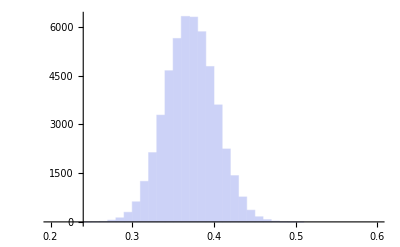

```mathematica
fsamples[i_] := Apply[f[i], parsamples, 1];
samples=Table[fsamples[i], {i, {15,19.21}}];
n=Length[samples]
hist[i_, p_List] := Histogram[samples[[i]], p]
hist[1, {0.2, 0.6, 0.01}]
```

```mathematica
fmean[i_] := Mean[samples[[i]]]
fcov[i_, j_] := Covariance[samples[[i]], samples[[j]]]
SetAttributes[fcov, Orderless]
```

```mathematica
fmeanvector = Table[fmean[i], {i, 1, n}]
```

{0.371041,0.440076}

Symmetrize covariance

```mathematica
fcovmatrix = Table[fcov[i, j], {i, 1, n}, {j, 1, n}];
fcovmatrix = (fcovmatrix + Transpose[fcovmatrix])/2;
fcovmatrix//MatrixForm
```

(0.000942159 | 0.000171851
0.000171851 | 0.000749573)

```mathematica
fsigvector = Table[Sqrt[fcovmatrix[[i]][[i]]], {i, 1, n}]
```

{0.0306946,0.0273783}

```mathematica
fcorrmatrix = Table[fcovmatrix[[i]][[j]] / Sqrt[fcovmatrix[[i]][[i]] fcovmatrix[[j]][[j]]], {i, 1, n}, {j, 1, n}]
fcorrmatrix // MatrixForm
```

{{1.,0.204495},{0.204495,1.}}

(1. | 0.204495
0.204495 | 1.)

```mathematica
dist = MultinormalDistribution[fmeanvector, fcovmatrix];
```

```mathematica
PDF[dist, fmeanvector]
```

193.476

```mathematica
Inverse[fcovmatrix]
Det[fcovmatrix]
```

{{1107.71,-253.96},{-253.96,1392.32}}

6.76684×10^-7

# Results from arXiv:1310.3722 v3

## Numerical input - see tables

```mathematica
mass[Bd]=5.279; (* [GeV] *)
mass[Bs]=5.366; 
mass[Kstar]=0.892;
mass[phi]=1.020;
```

pion decay constant [below eq.(39)]

```mathematica
fPi = 0.132; (* [GeV] *)
```

Δm for pole-masses entering blaschke factor from table V in GeV

```mathematica
Delm[Bd,Kstar,A0]=0.087;
Delm[Bd,Kstar,V|T1]= 0.135;
Delm[Bd,Kstar,A1|A12|T2|T23]=0.550;
Delm[Bs,phi,A0]=0.0;
Delm[Bs,phi,V|T1]= 0.045;
Delm[Bs,phi,A1|A12|T2|T23]=0.440;
Delm[Bs,Kstar,A0]=-0.087;
Delm[Bs,Kstar,V|T1]= -0.042;
Delm[Bs,Kstar,A1|A12|T2|T23]=0.350;
```

mean values, standard deviations and correlation matrices for B→K^*form factors for parameters {a_0,a_1}, see table VII

```mathematica
mean[Bd,Kstar,V]={0.496,-2.03};
std[Bd,Kstar,V]={0.067, 0.92};
cor[Bd, Kstar,V]={{1.0,0.86},{0.86,1.0}};
(* *)
mean[Bd,Kstar,A1]={0.286,0.19};
std[Bd,Kstar,A1]={0.024, 0.28};
cor[Bd, Kstar,A1]={{1.0,0.94},{0.94,1.0}};
(* *)
mean[Bd,Kstar,A12]={0.216,0.32};
std[Bd,Kstar,A12]={0.027, 0.38};
cor[Bd, Kstar,A12]={{1.0,0.91},{0.91,1.0}};
```

```mathematica
cov[B_,V_,FF_]:=Module[
{res},
len= Length[cor[B,V,FF]];
res=Table[cor[B,V,FF][[i,j]] std[B,V,FF][[i]]std[B,V,FF][[j]],{i,len},{j,len}]
]
```

## FF parametrization

Blaschke factor from eq.(38)

```mathematica
blaschke[t_,B_,V_,FF_]:= 1-t/(mass[B] + Delm[B,V,FF])^2
```

variable transformation from q^2→z  eq.(36), t_0= 12 GeV^2[see above eq.(37)]

```mathematica
t0 = 12.;
z[t_,B_,V_] := Module[
{tPlus,res},
tPlus = (mass[B] + mass[V])^2;
res =(Sqrt[tPlus - t] - Sqrt[tPlus - t0]) / (Sqrt[tPlus - t] + Sqrt[tPlus - t0])
]
```

Δx and Δx_s [see below eq.(39)] - not used, set to zero

general form factor parametrization eq.(42) for B→V with B = {B_d, B_s} and V = {K^*,ϕ } !!! not all combinations supported

```mathematica
ff[t_,B_,V_,FF_] := 1/blaschke[t, B,V,FF](a[B,V,FF,0](1.0)+ a[B,V,FF,1] z[t,B,V])
```

constant systematic uncertainty of 5% from table XII

```mathematica
sysffunc = 0.05;
```

```mathematica
q2max[B_,V_]:=(mass[B]-mass[V])^2;
```

## Generate form factors

generate form factor FF for transition B→V 
- at q^2 values in "q2List" 
- with (number of samples)=”Nsamples”
- numerical output with number of “digits”

```mathematica
genFF[B_,V_,FF_,q2List_,Nsamples_,digits_]:= Module[
{dist,pdf,n,parsamples,f,fsamples, samples,fmeanvector,fcov,fcovmatrix,fsigvector,fsigvectorFinal,fcorrmatrix},
(* *)
Print["\nForm factor ",FF," for ", B,"->",V," @ q^2 = ",q2List, " GeV^2"];
dist = MultinormalDistribution[mean[B,V,FF], cov[B,V,FF]];
pdf = PDF[dist, {a[B,V,FF,0], a[B,V,FF,1]}];
n = Length[q2List];
SeedRandom[1253457];
parsamples = RandomVariate[dist, Nsamples];
f[t_][a0_,a1_]:=ff[t,B,V,FF]//. {a[B,V,FF, 0]->a0,a[B,V,FF,1]->a1};
fsamples[t_]:= Apply[f[t], parsamples, 1];
samples=(fsamples[#])&/@ q2List;
fmeanvector= Table[Mean[samples[[i]]],{i, 1, n}];
fcov[i_, j_] := Covariance[samples[[i]], samples[[j]]];
SetAttributes[fcov, Orderless];
Print["Central values                         : ",NumberForm[fmeanvector, digits]];
fcovmatrix = Table[fcov[i, j], {i, 1, n}, {j, 1, n}];
fcovmatrix = (fcovmatrix + Transpose[fcovmatrix])/2;
fsigvector = Table[Sqrt[fcovmatrix[[i]][[i]]], {i, 1, n}];
Print["Standard deviations (no systematics)   : ",NumberForm[fsigvector, digits], " = ",NumberForm[100. fsigvector/fmeanvector, digits]," %"];
fsigvectorFinal = Sqrt[fsigvector^2+ (sysffunc fmeanvector)^2];
Print["Standard deviations (with systematics) : ",NumberForm[fsigvectorFinal, digits], " = ",NumberForm[100. fsigvectorFinal/fmeanvector, digits]," %"];
fcorrmatrix = Table[fcovmatrix[[i]][[j]] / Sqrt[fcovmatrix[[i]][[i]] fcovmatrix[[j]][[j]]], {i, 1, n}, {j, 1, n}];
Print["Correlation matrix : ", NumberForm[fcorrmatrix,digits-1]];
]
```

some checks with table XXXI - central values ok, standard deviations need inclusion of systematic uncertainties

```mathematica
checkq2List = {0.,12.,16.,q2max[Bd,Kstar]};
(genFF[Bd,Kstar,#,checkq2List, 100000,3])& /@ {V,A1,A12}
```

Form factor V for Bd->Kstar @ q^2 = {0.,12.,16.,19.2458} GeV^2

Central values                         : {0.304,0.839,1.28,1.92}

Standard deviations (no systematics)   : {0.149,0.114,0.0865,0.111} = {48.9,13.5,6.77,5.79} %

Standard deviations (with systematics) : {0.15,0.121,0.108,0.147} = {49.1,14.4,8.42,7.65} %

Correlation matrix : {{1.,0.95,0.68,-0.23},{0.95,1.,0.87,0.069},{0.68,0.87,1.,0.56},{-0.23,0.069,0.56,1.}}

Form factor A1 for Bd->Kstar @ q^2 = {0.,12.,16.,19.2458} GeV^2

Central values                         : {0.304,0.442,0.525,0.624}

Standard deviations (no systematics)   : {0.0498,0.0372,0.0258,0.0189} = {16.4,8.41,4.91,3.03} %

Standard deviations (with systematics) : {0.052,0.0432,0.0368,0.0365} = {17.1,9.78,7.01,5.85} %

Correlation matrix : {{1.,0.98,0.89,0.14},{0.98,1.,0.96,0.32},{0.89,0.96,1.,0.58},{0.14,0.32,0.58,1.}}

Form factor A12 for Bd->Kstar @ q^2 = {0.,12.,16.,19.2458} GeV^2

Central values                         : {0.246,0.334,0.383,0.438}

Standard deviations (no systematics)   : {0.0616,0.0418,0.0269,0.0296} = {25.,12.5,7.02,6.77} %

Standard deviations (with systematics) : {0.0628,0.045,0.033,0.0369} = {25.5,13.5,8.62,8.41} %

Correlation matrix : {{1.,0.97,0.75,-0.33},{0.97,1.,0.89,-0.087},{0.75,0.89,1.,0.38},{-0.33,-0.087,0.38,1.}}

{Null,Null,Null}

generate constraints for EOS

```mathematica
EOSq2List = {15., 19.21};
(genFF[Bd,Kstar,#,EOSq2List, 100000,3])& /@{V,A1,A12}
```

Form factor V for Bd->Kstar @ q^2 = {15.,19.21} GeV^2

Central values                         : {1.14,1.91}

Standard deviations (no systematics)   : {0.0926,0.11} = {8.1,5.77} %

Standard deviations (with systematics) : {0.109,0.146} = {9.52,7.63} %

Correlation matrix : {{1.,0.39},{0.39,1.}}

Form factor A1 for Bd->Kstar @ q^2 = {15.,19.21} GeV^2

Central values                         : {0.502,0.623}

Standard deviations (no systematics)   : {0.0291,0.0188} = {5.8,3.03} %

Standard deviations (with systematics) : {0.0384,0.0364} = {7.66,5.84} %

Correlation matrix : {{1.,0.5},{0.5,1.}}

Form factor A12 for Bd->Kstar @ q^2 = {15.,19.21} GeV^2

Central values                         : {0.369,0.437}

Standard deviations (no systematics)   : {0.0307,0.0294} = {8.31,6.72} %

Standard deviations (with systematics) : {0.0358,0.0366} = {9.7,8.37} %

Correlation matrix : {{1.,0.21},{0.21,1.}}

{Null,Null,Null}

# Results from arXiv:1501.00367 v2

Provide now simultaneous fit of 
i = vector) vector FF V and axial-vector FF’s A_(0,1,2)
i = tensor) tensor FF’s T_(1,2,3)

## Numerical Input

meson masses

```mathematica
mass[Bd]=5.279; (* [GeV] *)
mass[Bs]=5.366; 
mass[Kstar]=0.892;
mass[phi]=1.020;
```

pion decay constant [below eq.(39)]

```mathematica
fPi = 0.132; (* [GeV] *)
```

Δm for pole-masses entering blaschke factor from table 4 in GeV

```mathematica
Delm[Bd,Kstar,A0]=0.087;
Delm[Bd,Kstar,V|T1]= 0.135;
Delm[Bd,Kstar,A1|A12|T2|T23]=0.550;
Delm[Bs,phi,A0]=0.0;
Delm[Bs,phi,V|T1]= 0.045;
Delm[Bs,phi,A1|A12|T2|T23]=0.440;
Delm[Bs,Kstar,A0]=-0.087;
Delm[Bs,Kstar,V|T1]= -0.042;
Delm[Bs,Kstar,A1|A12|T2|T23]=0.350;
```

mean values, standard deviations and correlation matrices for
1)  B→K^*FFs of parameters {a_0,a_1}, see ancillary files av_sl_results.d, av_sl_covariance.d

```mathematica
mean[Bd,Kstar,vector]={
0.497528420813,-2.0150648425,0.502302643141,-1.60847600112,
0.284803612469,0.191411584999,0.219527522577,0.332374417965
};
covUpperTriangleMat[Bd, Kstar,vector]={
{0.00444654018992,0.0524970754225,2.37306288148 10^(-20),-2.95976605864 10^(-19),
9.33920040692  10^(-20), 5.44187127382 10^(-19),1.77329950593 10^(-20),-2.19702205261 10^(-19)},
{0.839955459133,1.17941203146  10^(-18),6.43096859783 10^(-18),1.30609221482 10^(-18),
8.89537194192 10^(-18),8.16117124897 10^(-19),4.89571706323 10^(-18)},
{0.00136946827176,0.0110440703514,1.31321639273 10^(-7),-4.09678532204 10^(-7),
0.000794991170373,0.00986195471942},
{0.200005848693,-0.000417726083314,0.0013031622938,0.00965835763816,
0.124472699853},
{0.000543873928258,0.00620191457205,4.02729647337 10^(-6),-0.00034059829966},
{0.078649854783,-1.25637855037 10^(-5),0.00106255002783},
{0.00056438444752,0.00695753530286},
{0.0901066592905}
};
```

see ancillary files t_sl_results.d, t_sl_covariance.d

```mathematica
mean[Bd,Kstar,tensor]={
0.419712711234,-1.36328797303,0.279965680646,
0.11706607999,0.523462757534,-0.27135970224
};
covUpperTriangleMat[Bd, Kstar,tensor]={
{0.000578803972895,0.00311342645125,0.000398503077207,0.00466585264398,6.91175406734 10^(-6),-0.000475345379278},{0.0668607343908,0.00403734128983,0.0511218767784,-2.55954151772 10^(-5),0.00176028577067},
{0.000379492472464,0.00429334278455,1.03047879282 10^(-5),-0.000708696125234},
{0.0558754013656,-6.4761686916 10^(-5),0.00445388657204},
{0.00203658876913,0.0248795682942},
{0.335383041904}
};
```

2)  B_s→ϕ FFs of parameters {a_0,a_1}, see tables 5 and 6

3)  B_s→K^*FFs of parameters {a_0,a_1}, see tables 5 and 6

generate covariance matrices from Upper Triangle matrices

```mathematica
cov[Bq_,VV_,FFtype_]:=Module[
{res,len},
len = Length[covUpperTriangleMat[Bq,VV,FFtype]];
res=DiagonalMatrix[Table[1,{i,len}]];
Do[Do[
k=j-(i-1);
res[[i,j]]=covUpperTriangleMat[Bq,VV,FFtype][[i,k]];
res[[j,i]]=res[[i,j]],
{j,i,len}],{i,len}
];
res=res
]
```

## FF parameterization - eq-numbers refer to arXiv:1310.3722

Blaschke factor from eq.(38)

```mathematica
blaschke[t_,Bq_,VV_,FF_]:=
 1-t/(mass[Bq] + Delm[Bq,VV,FF])^2
```

variable transformation from q^2→z  eq.(36), t_0= 12 GeV^2[see above eq.(37)]

```mathematica
t0 = 12.;
z[t_,Bq_,VV_] := Module[
{tPlus,res},
tPlus = (mass[Bq] + mass[VV])^2;
res =(Sqrt[tPlus - t] - Sqrt[tPlus - t0]) / (Sqrt[tPlus - t] + Sqrt[tPlus - t0])
]
```

Δx and Δx_s [see below eq.(39)] - not used, set to zero

general form factor parametrization eq.(42) for B→V with B = {B_d, B_s} and V = {K^*,ϕ } !!! not all combinations supported

```mathematica
ff[t_,Bq_,VV_,FF_]:=
1/blaschke[t, Bq,VV,FF](a[Bq,VV,FF,0](1.0)+ a[Bq,VV,FF,1] z[t,Bq,VV])
```

constant systematic uncertainty of 5% from table XII

```mathematica
sysffunc = 0.05;
```

```mathematica
q2max[Bq_,VV_]:=(mass[Bq]-mass[VV])^2;
```

## Generate form factors

generate FF’s ={FF_1, ... FF_N} for transitions: B_q → V

- at q^2 values in "q2List = {q_1^2, ... q_M^2}"
- with (number of samples)=”Nsamples”
- numerical output with number of “digits”
- test whether covariance matrix positive definite and invertable, otherwise correlation can not be used in EOS

outputs are

1) mean value
2) standard deviation
    a) without systematic uncertainty
    b) with systematic ⟸ this one should be used
3) correlation matrix 

for 

  {FF_1(q_1^2),FF_2(q_1^2)...FF_N(q_1^2),   ...   FF_1(q_M^2),FF_2(q_M^2)...FF_N(q_M^2)}

```mathematica
genFF[Bq_,VV_,FFtype_,q2List_,Nsamples_,digits_]:= Module[
{dist,parsamples,f, samples,fmeanvector,fcov,fcovmatrix,fsigvector,fsigvectorFinal,fcorrmatrix},
(* *)
Print["\nFF's ",FFtype," for ", Bq,"->",VV," @ q^2 = ",q2List, " GeV^2"];
f[vector][Va0_,Va1_,A0a0_,A0a1_,A1a0_,A1a1_,A12a0_,A12a1_]:=Module[
{res},
res ={
ff[#,Bq,VV,V]//. {a[Bq,VV,V, 0]->Va0,a[Bq,VV,V,1]->Va1},
ff[#,Bq,VV,A0]//. {a[Bq,VV,A0, 0]->A0a0,a[Bq,VV,A0,1]->A0a1},
ff[#,Bq,VV,A1]//. {a[Bq,VV,A1, 0]->A1a0,a[Bq,VV,A1,1]->A1a1},
ff[#,Bq,VV,A12]//. {a[Bq,VV,A12, 0]->A12a0,a[Bq,VV,A12,1]->A12a1}
}&/@ q2List;
res = Join@@res
];
f[tensor][T1a0_,T1a1_,T2a0_,T2a1_,T23a0_,T23a1_]:=Module[
{res},
res={
ff[#,Bq,VV,T1]//. {a[Bq,VV,T1, 0]->T1a0,a[Bq,VV,T1,1]->T1a1},
ff[#,Bq,VV,T2]//. {a[Bq,VV,T2, 0]->T2a0,a[Bq,VV,T2,1]->T2a1},
ff[#,Bq,VV,T23]//. {a[Bq,VV,T23, 0]->T23a0,a[Bq,VV,T23,1]->T23a1}
}&/@q2List;
res=Join@@res
];
Switch[FFtype,
vector,n=4 Length[q2List],
tensor,n=3 Length[q2List]
];
dist = MultinormalDistribution[mean[Bq,VV,FFtype], cov[Bq,VV,FFtype]];
SeedRandom[1253457];
parsamples = RandomVariate[dist, Nsamples];
samples= Apply[f[FFtype], parsamples, 1];
samples=Transpose[samples];
fmeanvector= Table[Mean[samples[[i]]],{i, 1, n}];
fcov[i_, j_] := Covariance[samples[[i]], samples[[j]]];
SetAttributes[fcov, Orderless];
Print["Central values                         : ",NumberForm[fmeanvector, digits]];
fcovmatrix = Table[fcov[i, j], {i, 1, n}, {j, 1, n}];
(* enforce symmetric covariance matrix *)
fcovmatrix = (fcovmatrix + Transpose[fcovmatrix])/2;
Print["\nDet[fcovmatrix] = ",Det[fcovmatrix]];
Print["\nInverse covariance = ",Inverse[fcovmatrix]];
fsigvector = Table[Sqrt[fcovmatrix[[i]][[i]]], {i, 1, n}];
Print["Standard deviations (no systematics)   : ",NumberForm[fsigvector, digits],
"\n                                       = ",NumberForm[100. fsigvector/fmeanvector, digits]," %"];
fsigvectorFinal = Sqrt[fsigvector^2+ (sysffunc fmeanvector)^2];
Print["Standard deviations (with systematics) : ",NumberForm[fsigvectorFinal, digits],
"\n                                       = ",NumberForm[100. fsigvectorFinal/fmeanvector, digits]," %"];
fcorrmatrix = Table[fcovmatrix[[i]][[j]] / Sqrt[fcovmatrix[[i]][[i]] fcovmatrix[[j]][[j]]], {i, 1, n}, {j, 1, n}];
Print["Correlation matrix : ", MatrixForm[NumberForm[fcorrmatrix,digits-1]]];
]
```

checks with table 11 - central values and standard deviations need inclusion of systematic uncertainties -> agree very well

```mathematica
checkq2List = {0.,12.,16.,q2max[Bd,Kstar]};
(genFF[Bd,Kstar,#,checkq2List, 50000,3])& /@ {vector, tensor}
```

FF's vector for Bd->Kstar @ q^2 = {0.,12.,16.,19.2458} GeV^2

Central values                         : {0.306,0.351,0.303,0.251,0.841,0.861,0.44,0.34,1.28,1.28,0.523,0.389,1.92,1.91,0.621,0.444}

Det[fcovmatrix] = -5.16056×10^-174

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0217409, 0.0000928859, 0.0000311284, 0.0000665385, 0.0158466, 0.0000946571, 0.0000185002, 0.0000447707, 0.00858719, 0.0000868634, 6.64813×10^-6, 0.0000234159, -0.00377462, 0.0000687102, -0.0000104339, -7.79796×10^-6}, {« 1 »}, « 13 », {-7.79796×10^-6, -0.0001168, 0.000052033, -0.0000835798, « 8 », -1.99393×10^-6, 0.000213254, 0.000209259, 0.000150707}} may contain significant numerical errors.

Inverse covariance = {{-1.4965×10^16,-1.02263×10^16,1.33282×10^17,-1.17968×10^16,9.44105×10^16,1.29585×10^16,-1.22045×10^15,-3.28273×10^16,-1.18739×10^17,-9.87384×10^13,-3.10609×10^17,8.27389×10^16,4.00309×10^16,-3.90279×10^15,1.9756×10^17,-4.06815×10^16},{-1.33752×10^16,-8.80153×10^16,2.18613×10^18,-4.10511×10^17,-3.41446×10^16,1.18396×10^17,1.96181×10^16,5.56983×10^16,8.07714×10^16,-1.15745×10^16,-5.16117×10^18,8.69555×10^17,-3.66303×10^16,-2.94896×10^16,3.26834×10^18,-5.71908×10^17},{9.78671×10^16,1.43422×10^18,-1.94372×10^19,-1.19388×10^18,3.26177×10^17,-2.37696×10^18,5.29593×10^17,5.14354×10^18,-7.11384×10^17,8.87983×10^17,4.47078×10^19,-5.82737×10^18,3.14662×10^17,2.13115×10^17,-2.85635×10^19,1.84512×10^18},{9.79683×10^14,-3.19931×10^17,-1.53196×10^18,-4.54404×10^17,2.65495×10^16,1.93333×10^17,3.52183×10^16,-8.62395×10^15,-4.3837×10^16,3.28227×10^17,3.53462×10^18,1.08042×10^18,1.73745×10^16,-2.48786×10^17,-2.25585×10^18,-6.82553×10^17},{1.00367×10^17,-2.6877×10^16,4.1257×10^17,2.05336×10^16,-1.18574×10^17,4.78272×10^16,-6.14851×10^15,-1.01089×10^17,-1.51133×10^16,-2.17704×10^16,-9.57501×10^17,1.21402×10^17,4.59063×10^16,-2.03221×10^15,6.09869×10^17,-4.06256×10^16},{1.50389×10^16,1.03581×10^17,-2.63778×10^18,2.22223×10^17,4.43395×10^16,-2.5037×10^17,-8.81361×10^15,-2.13485×10^17,-1.00197×10^17,1.87087×10^17,6.20254×10^18,-1.63188×10^17,4.48201×10^16,-3.16237×10^16,-3.93311×10^18,1.80475×10^17},{4.82456×10^16,7.58013×10^17,-9.4528×10^18,-5.59321×10^17,1.6256×10^17,-1.23641×10^18,-9.92705×10^17,2.68534×10^18,-3.53473×10^17,4.38296×10^17,2.38398×10^19,-3.19243×10^18,1.56197×10^17,1.24496×10^17,-1.47717×10^19,1.05855×10^18},{-3.51918×10^16,-3.43523×10^15,6.06196×10^18,3.46753×10^17,-1.01863×10^17,-5.17553×10^16,-2.27582×10^15,1.92094×10^17,2.3148×10^17,8.76219×10^16,-1.42165×10^19,-1.13565×10^18,-1.03725×10^17,-3.4828×10^16,9.02294×10^18,6.51504×10^17},{-1.28131×10^17,6.29713×10^16,-9.18919×10^17,-8.62584×10^15,-3.12051×10^15,-1.01508×10^17,1.21526×10^16,2.25498×10^17,2.6291×10^17,3.45274×10^16,2.13523×10^18,-3.58026×10^17,-1.52988×10^17,1.10627×10^16,-1.35945×10^18,1.45972×10^17},{2.85446×10^15,1.15703×10^16,-1.85787×10^17,4.61535×10^17,-2.00463×10^15,1.57901×10^17,-2.48784×10^16,2.23791×10^17,-2.58641×10^15,-2.69474×10^17,4.77556×10^17,-1.45807×10^18,2.14111×10^15,1.07498×10^17,-2.94106×10^17,8.44705×10^17},{-3.10508×10^17,-4.63596×10^18,6.14527×10^19,3.73885×10^18,-1.03784×10^18,7.64991×10^18,4.22874×10^17,-1.65703×10^19,2.26171×10^18,-2.81827×10^18,-1.44866×10^20,1.90251×10^19,-1.00015×10^18,-7.08765×10^17,9.17835×10^19,-6.10398×10^18},{5.6734×10^16,7.56264×10^17,-6.57489×10^18,4.84294×10^17,1.08589×10^17,-3.66708×10^17,-7.87982×10^16,-3.01997×10^17,-2.85461×10^17,-9.16943×10^17,1.55557×10^19,-6.29486×10^17,1.33235×10^17,6.4203×10^17,-9.84364×10^18,5.08288×10^17},{4.36696×10^16,-2.84775×10^16,4.092×10^17,-1.36557×10^15,3.88831×10^16,4.44978×10^16,-5.19526×10^15,-1.00464×10^17,-1.49241×10^17,-1.34162×10^16,-9.51194×10^17,1.71725×10^17,7.52459×10^16,-5.84336×10^15,6.05523×10^17,-7.2787×10^16},{-6.24538×10^15,-3.83395×10^16,9.13432×10^17,-3.34663×10^17,-1.23906×10^16,-1.47552×10^16,1.70724×10^16,-6.41092×10^16,3.2113×10^16,9.85795×10^16,-2.17138×10^18,8.92599×10^17,-1.49336×10^16,-5.24678×10^16,1.37186×10^18,-5.43369×10^17},{1.79675×10^17,2.669×10^18,-3.55939×10^19,-2.17126×10^18,6.00072×10^17,-4.40939×10^18,8.92766×10^16,9.5485×10^18,-1.30799×10^18,1.63064×10^18,8.33471×10^19,-1.09237×10^19,5.78449×10^17,4.04948×10^17,-5.29263×10^19,3.49238×10^18},{-2.33262×10^16,-4.78707×10^17,1.98864×10^18,-4.3227×10^17,-3.22151×10^16,2.51368×10^17,5.08273×10^16,1.22449×10^17,9.77651×10^16,5.50348×10^17,-4.75025×10^18,8.08628×10^17,-4.71851×10^16,-3.94901×10^17,2.99632×10^18,-5.5729×10^17}}

Standard deviations (no systematics)   : {0.147,0.0724,0.049,0.0518,0.113,0.0635,0.036,0.0367,0.0863,0.0635,0.0242,0.0224,0.112,0.0903,0.0171,0.0123}
                                       = {48.1,20.6,16.2,20.6,13.4,7.37,8.17,10.8,6.75,4.96,4.62,5.77,5.81,4.73,2.75,2.76} %

Standard deviations (with systematics) : {0.148,0.0745,0.0513,0.0533,0.12,0.0767,0.0422,0.0405,0.107,0.0902,0.0356,0.0297,0.147,0.131,0.0354,0.0254}
                                       = {48.4,21.2,16.9,21.2,14.3,8.9,9.58,11.9,8.4,7.04,6.8,7.64,7.66,6.88,5.71,5.71} %

Correlation matrix : {{1.,0.0087,0.0043,0.0087,0.95,0.01,0.0035,0.0083,0.67,0.0093,0.0019,0.0071,-0.23,0.0052,-0.0041,-0.0043},{0.0087,1.,-0.013,1.,0.0054,0.9,-0.029,0.99,-0.0011,0.57,-0.055,0.94,-0.011,-0.011,-0.099,-0.13},{0.0043,-0.013,1.,-0.013,0.0011,-0.0006,0.99,-0.0024,-0.0044,0.013,0.89,0.018,-0.011,0.025,0.064,0.086},{0.0087,1.,-0.013,1.,0.0055,0.9,-0.029,0.99,-0.0011,0.57,-0.055,0.94,-0.011,-0.011,-0.099,-0.13},{0.95,0.0054,0.0011,0.0055,1.,0.0066,0.00027,0.0049,0.87,0.0063,-0.0012,0.0037,0.075,0.0038,-0.0047,-0.0049},{0.01,0.9,-0.0006,0.9,0.0066,1.,-0.0016,0.9,-0.00064,0.87,-0.0031,0.87,-0.012,0.42,-0.0057,-0.035},{0.0035,-0.029,0.99,-0.029,0.00027,-0.0016,1.,0.0012,-0.0051,0.03,0.96,0.06,-0.011,0.057,0.23,0.25},{0.0083,0.99,-0.0024,0.99,0.0049,0.9,0.0012,1.,-0.0017,0.58,0.0072,0.97,-0.011,0.012,0.021,-0.012},{0.67,-0.0011,-0.0044,-0.0011,0.87,-0.00064,-0.0051,-0.0017,1.,0.000031,-0.006,-0.0027,0.56,0.00081,-0.0047,-0.0048},{0.0093,0.57,0.013,0.57,0.0063,0.87,0.03,0.58,0.000031,1.,0.057,0.59,-0.01,0.82,0.1,0.082},{0.0019,-0.055,0.89,-0.055,-0.0012,-0.0031,0.96,0.0072,-0.006,0.057,1.,0.13,-0.01,0.11,0.5,0.52},{0.0071,0.94,0.018,0.94,0.0037,0.87,0.06,0.97,-0.0027,0.59,0.13,1.,-0.011,0.056,0.25,0.22},{-0.23,-0.011,-0.011,-0.011,0.075,-0.012,-0.011,-0.011,0.56,-0.01,-0.01,-0.011,1.,-0.0047,-0.0016,-0.0015},{0.0052,-0.011,0.025,-0.011,0.0038,0.42,0.057,0.012,0.00081,0.82,0.11,0.056,-0.0047,1.,0.19,0.19},{-0.0041,-0.099,0.064,-0.099,-0.0047,-0.0057,0.23,0.021,-0.0047,0.1,0.5,0.25,-0.0016,0.19,1.,1.},{-0.0043,-0.13,0.086,-0.13,-0.0049,-0.035,0.25,-0.012,-0.0048,0.082,0.52,0.22,-0.0015,0.19,1.,1.}}

FF's tensor for Bd->Kstar @ q^2 = {0.,12.,16.,19.2458} GeV^2

Central values                         : {0.291,0.291,0.498,0.71,0.433,0.809,1.05,0.52,1.01,1.54,0.624,1.26}

Det[fcovmatrix] = -1.22532×10^-131

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00175618, 0.00167311, -5.32868×10^-6, 0.00146972, 0.0012057, 0.0000243758, 0.00104907, 0.00072961, 0.000047379, 0.000302005, 0.0000258127, 0.000078236}, « 10 », {0.000078236, 0.0000721421, -0.000455852, 0.000184367, 0.000247843, 0.0000713294, 0.000269528, 0.000376463, 0.000505525, 0.000393897, 0.000544746, 0.00110278}} may contain significant numerical errors.

Inverse covariance = {{3.69191×10^17,-6.42593×10^17,1.54112×10^16,-4.97691×10^17,1.49825×10^16,-1.06177×10^17,4.14225×10^16,1.48228×10^18,1.41954×10^17,1.31276×10^17,-9.46088×10^17,-5.18349×10^16},{-8.93223×10^17,1.2×10^18,-8.01865×10^16,1.17987×10^18,-2.35651×10^18,1.4482×10^17,-6.19794×10^16,1.13792×10^18,-5.4824×10^16,-3.32425×10^17,1.26829×10^17,-1.73818×10^16},{-2.62816×10^16,1.73654×10^16,-3.66047×10^17,1.54375×10^16,-1.62789×10^16,3.57052×10^17,2.85749×10^16,-1.34292×10^16,2.59747×10^17,-2.15583×10^16,1.43873×10^16,-2.93477×10^17},{-5.54817×10^17,9.69748×10^17,-5.56833×10^16,5.72878×10^17,-4.57232×10^17,1.86558×10^17,2.13772×10^17,-1.50787×10^18,-1.82317×10^17,-3.04219×10^17,1.12166×10^18,4.84917×10^16},{4.70654×10^17,-2.9337×10^18,1.6983×10^17,-1.0249×10^18,5.18629×10^18,-3.20815×10^17,6.68459×10^17,-1.81777×10^18,1.39758×10^17,-7.11662×10^16,-7.14868×10^17,2.68863×10^16},{-3.5756×10^16,-1.42665×10^16,1.10668×10^17,5.78685×10^16,1.42615×10^15,2.75368×10^17,-1.92557×10^16,3.10743×10^16,-7.21521×10^17,-6.80813×10^15,-2.02343×10^16,3.58688×10^17},{1.31502×10^17,-2.35294×10^17,5.67738×10^16,9.87495×10^16,6.90817×10^17,-8.03881×10^16,-4.20489×10^17,-6.06848×10^17,1.66519×10^15,2.15384×10^17,1.3624×10^17,2.79047×10^16},{1.30585×10^18,2.10612×10^18,-9.67765×10^16,-1.04854×10^18,-3.17176×10^18,1.98427×10^17,-9.75909×10^17,3.79848×10^17,-1.05829×10^17,8.99186×10^17,9.0163×10^17,-4.32572×10^15},{1.21631×10^17,-1.6805×10^16,6.73042×10^17,-1.33285×10^17,3.57951×10^16,-1.29949×10^18,-3.47314×10^16,-2.06228×10^16,6.00989×10^17,6.19921×10^16,1.91782×10^14,8.67672×10^16},{9.63771×10^16,-1.65265×10^17,-1.58459×10^16,-2.3686×10^17,-2.61662×10^17,-1.12251×10^16,1.79438×10^17,8.26605×10^17,5.6001×10^16,-3.10601×10^16,-4.30315×10^17,-3.14956×10^16},{-9.98287×10^17,-2.79672×10^17,2.31994×10^14,1.03467×10^18,1.44405×10^17,-1.03461×10^16,3.7851×10^17,4.13829×10^17,1.68108×10^16,-5.45007×10^17,-3.14651×10^17,-6.94115×10^15},{-6.4308×10^16,1.58047×10^16,-4.67×10^17,6.37374×10^16,-2.32303×10^16,7.25484×10^17,2.89787×10^16,1.89258×10^15,-1.2146×10^17,-3.6889×10^16,7.16813×10^15,-1.8429×10^17}}

Standard deviations (no systematics)   : {0.0419,0.0411,0.0983,0.0407,0.0302,0.0696,0.046,0.0207,0.0442,0.0663,0.0164,0.0332}
                                       = {14.4,14.1,19.7,5.73,6.97,8.6,4.39,3.98,4.37,4.29,2.63,2.64} %

Standard deviations (with systematics) : {0.0444,0.0436,0.101,0.054,0.0371,0.0805,0.0697,0.0332,0.0671,0.102,0.0352,0.0711}
                                       = {15.3,15.,20.3,7.6,8.58,9.95,6.65,6.39,6.64,6.59,5.65,5.65} %

Correlation matrix : {{1.,0.97,-0.0013,0.86,0.95,0.0084,0.54,0.84,0.026,0.11,0.038,0.056},{0.97,1.,-0.003,0.85,0.98,0.0061,0.54,0.86,0.022,0.12,0.034,0.053},{-0.0013,-0.003,1.,-0.016,-0.026,0.99,-0.026,-0.062,0.88,-0.03,-0.12,-0.14},{0.86,0.85,-0.016,1.,0.85,0.0068,0.89,0.78,0.049,0.6,0.12,0.14},{0.95,0.98,-0.026,0.85,1.,0.016,0.56,0.95,0.093,0.15,0.23,0.25},{0.0084,0.0061,0.99,0.0068,0.016,1.,0.0039,0.032,0.95,0.00019,0.054,0.031},{0.54,0.54,-0.026,0.89,0.56,0.0039,1.,0.54,0.059,0.89,0.17,0.18},{0.84,0.86,-0.062,0.78,0.95,0.032,0.54,1.,0.2,0.19,0.53,0.55},{0.026,0.022,0.88,0.049,0.093,0.95,0.059,0.2,1.,0.057,0.37,0.34},{0.11,0.12,-0.03,0.6,0.15,0.00019,0.89,0.19,0.057,1.,0.18,0.18},{0.038,0.034,-0.12,0.12,0.23,0.054,0.17,0.53,0.37,0.18,1.,1.},{0.056,0.053,-0.14,0.14,0.25,0.031,0.18,0.55,0.34,0.18,1.,1.}}

{Null,Null}

generate constraints for EOS
!!! covariance matrix will be only positive definite for q^2= {15, 19.21} GeV^2 - choosing narrower interval or three points does not work

```mathematica
EOSq2List = {15.,19.21};
(genFF[Bd,Kstar,#,EOSq2List, 100000,6])& /@{vector, tensor}
```

FF's vector for Bd->Kstar @ q^2 = {15.,19.21} GeV^2

Central values                         : {1.14464,1.15119,0.49946,0.37489,1.91508,1.89931,0.619687,0.443332}

Det[fcovmatrix] = 2.25842×10^-31

Inverse covariance = {{139.186,-316.594,-0.734008,515.867,-45.6437,157.034,-107.903,-134.397},{-316.594,2.04936×10^7,118.134,-3.33937×10^7,-95.985,-1.01565×10^7,38033.4,1.84814×10^7},{-0.734008,118.134,1670.11,-322.053,-1.18288,-57.0705,28401.4,-41081.2},{515.867,-3.33937×10^7,-322.053,5.44156×10^7,155.904,1.65498×10^7,-103307.,-3.00577×10^7},{-45.6437,-95.985,-1.18288,155.904,97.0768,47.3899,116.196,-248.127},{157.034,-1.01565×10^7,-57.0705,1.65498×10^7,47.3899,5.03368×10^6,-18801.8,-9.15959×10^6},{-107.903,38033.4,28401.4,-103307.,116.196,-18801.8,9.6953×10^6,-1.35109×10^7},{-134.397,1.84814×10^7,-41081.2,-3.00577×10^7,-248.127,-9.15959×10^6,-1.35109×10^7,3.55993×10^7}}

Standard deviations (no systematics)   : {0.0921677,0.0618387,0.0277005,0.0266435,0.110361,0.0898203,0.0171859,0.0123107}
                                       = {8.0521,5.37174,5.54609,7.10701,5.76275,4.72911,2.77332,2.77685} %

Standard deviations (with systematics) : {0.108491,0.0844814,0.0372957,0.0325766,0.146111,0.130714,0.0354314,0.0253557}
                                       = {9.47821,7.33863,7.4672,8.68963,7.6295,6.88219,5.71763,5.71934} %

Correlation matrix : {{1.,0.00052981,0.0021485,0.0010579,0.39269,-0.00047199,-0.00053295,-0.00055847},{0.00052981,1.,0.031735,0.70766,0.0013494,0.71678,0.0757,0.071136},{0.0021485,0.031735,1.,0.070338,0.0044106,0.08122,0.4188,0.42273},{0.0010579,0.70766,0.070338,1.,0.000593,0.046446,0.16102,0.15462},{0.39269,0.0013494,0.0044106,0.000593,1.,0.001416,0.00050542,0.00057568},{-0.00047199,0.71678,0.08122,0.046446,0.001416,1.,0.19819,0.19814},{-0.00053295,0.0757,0.4188,0.16102,0.00050542,0.19819,1.,0.9998},{-0.00055847,0.071136,0.42273,0.15462,0.00057568,0.19814,0.9998,1.}}

FF's tensor for Bd->Kstar @ q^2 = {15.,19.21} GeV^2

Central values                         : {0.944705,0.494866,0.952108,1.53683,0.622428,1.25483}

Det[fcovmatrix] = 2.23591×10^-24

Inverse covariance = {{29560.6,-33599.1,-9.50455,-14741.9,28559.5,-5063.29},{-33599.1,41161.7,-331.865,16660.3,195597.,-108028.},{-9.50455,-331.865,566.573,3.77149,-113699.,56253.4},{-14741.9,16660.3,3.77149,7595.96,-14631.6,2658.92},{28559.5,195597.,-113699.,-14631.6,7.58273×10^7,-3.76041×10^7},{-5063.29,-108028.,56253.4,2658.92,-3.76041×10^7,1.86526×10^7}}

Standard deviations (no systematics)   : {0.0435124,0.02334,0.0516476,0.0656154,0.0163629,0.0330106}
                                       = {4.60593,4.71643,5.42455,4.26954,2.62889,2.63069} %

Standard deviations (with systematics) : {0.0642223,0.0340145,0.0702407,0.101044,0.0351609,0.0708956}
                                       = {6.79813,6.87348,7.37738,6.57488,5.64899,5.64983} %

Correlation matrix : {{1.,0.65399,0.041249,0.82578,0.16258,0.16507},{0.65399,1.,0.10027,0.1903,0.42549,0.429},{0.041249,0.10027,1.,0.046927,0.23557,0.23111},{0.82578,0.1903,0.046927,1.,0.18144,0.18189},{0.16258,0.42549,0.23557,0.18144,1.,0.99996},{0.16507,0.429,0.23111,0.18189,0.99996,1.}}

{Null,Null}

## LCSR

Remove rows and columns of ensor form factors, we only want vector FF

```mathematica
res=ReadList[FileNameJoin[{NotebookDirectory[],"InputData_BtoKstar_LCSR_StandardBasis.dat"}]];
indexList={1,2,3,4,8,9,10,11,15,16,17,18,22,23,24,25};
Length[indexList]
q2List=res[[1,1]]
mean =res[[1,2,1,#]]&/@indexList
unc=res[[1,2,2,#]]&/@indexList
corr=res[[1,2,3,#]]&/@indexList;
corr=(Transpose[corr])[[#]]&/@ indexList;
corr//MatrixForm
```

16

{0.1,2.1,4.1,6.1}

{0.393136,0.440394,0.496878,0.565342,0.337861,0.248569,0.272718,0.300677,0.463812,0.527595,0.3094,0.346962,0.322844,0.339239,0.358183,0.184952}

{0.0355001,0.0379432,0.0409139,0.0447278,0.0277636,0.0425329,0.0464452,0.0513414,0.0412791,0.0451053,0.0312183,0.0334351,0.0310408,0.0310295,0.0311597,0.0362825}

(1. | 0.996223 | 0.98192 | 0.951578 | -0.103402 | -0.45574 | -0.467341 | -0.479343 | -0.0405285 | -0.0210851 | -0.0100513 | 0.00483794 | 0.00384812 | 0.0159353 | 0.0280488 | -0.212172
0.996223 | 1. | 0.994645 | 0.974648 | -0.0768082 | -0.438892 | -0.450485 | -0.462993 | -0.00746895 | 0.0165039 | 0.0104096 | 0.029178 | 0.0276887 | 0.0431559 | 0.0588293 | -0.186504
0.98192 | 0.994645 | 1. | 0.992546 | -0.0445637 | -0.414755 | -0.426213 | -0.439188 | 0.0319558 | 0.0611947 | 0.0341161 | 0.057366 | 0.0552962 | 0.0747102 | 0.0945702 | -0.154476
0.951578 | 0.974648 | 0.992546 | 1. | -0.0058942 | -0.38069 | -0.391813 | -0.405139 | 0.0782278 | 0.113437 | 0.0609704 | 0.0892566 | 0.0865341 | 0.110452 | 0.135137 | -0.115049
-0.103402 | -0.0768082 | -0.0445637 | -0.0058942 | 1. | 0.900459 | 0.908151 | 0.911946 | 0.881278 | 0.882091 | 0.855073 | 0.868702 | 0.871919 | 0.887342 | 0.899462 | 0.801732
-0.45574 | -0.438892 | -0.414755 | -0.38069 | 0.900459 | 1. | 0.998098 | 0.991024 | 0.807463 | 0.777127 | 0.809184 | 0.800943 | 0.803166 | 0.794411 | 0.779673 | 0.826737
-0.467341 | -0.450485 | -0.426213 | -0.391813 | 0.908151 | 0.998098 | 1. | 0.997371 | 0.801602 | 0.775839 | 0.79853 | 0.792933 | 0.795599 | 0.790462 | 0.780002 | 0.819308
-0.479343 | -0.462993 | -0.439188 | -0.405139 | 0.911946 | 0.991024 | 0.997371 | 1. | 0.789007 | 0.768464 | 0.780879 | 0.778155 | 0.78139 | 0.780342 | 0.774784 | 0.804851
-0.0405285 | -0.00746895 | 0.0319558 | 0.0782278 | 0.881278 | 0.807463 | 0.801602 | 0.789007 | 1. | 0.993925 | 0.897145 | 0.910936 | 0.909425 | 0.918749 | 0.922113 | 0.836488
-0.0210851 | 0.0165039 | 0.0611947 | 0.113437 | 0.882091 | 0.777127 | 0.775839 | 0.768464 | 0.993925 | 1. | 0.867514 | 0.888839 | 0.887469 | 0.905531 | 0.919174 | 0.807209
-0.0100513 | 0.0104096 | 0.0341161 | 0.0609704 | 0.855073 | 0.809184 | 0.79853 | 0.780879 | 0.897145 | 0.867514 | 1. | 0.997409 | 0.996641 | 0.987453 | 0.968407 | 0.93369
0.00483794 | 0.029178 | 0.057366 | 0.0892566 | 0.868702 | 0.800943 | 0.792933 | 0.778155 | 0.910936 | 0.888839 | 0.997409 | 1. | 0.99916 | 0.995573 | 0.982884 | 0.930333
0.00384812 | 0.0276887 | 0.0552962 | 0.0865341 | 0.871919 | 0.803166 | 0.795599 | 0.78139 | 0.909425 | 0.887469 | 0.996641 | 0.99916 | 1. | 0.996686 | 0.984388 | 0.930968
0.0159353 | 0.0431559 | 0.0747102 | 0.110452 | 0.887342 | 0.794411 | 0.790462 | 0.780342 | 0.918749 | 0.905531 | 0.987453 | 0.995573 | 0.996686 | 1. | 0.99543 | 0.920883
0.0280488 | 0.0588293 | 0.0945702 | 0.135137 | 0.899462 | 0.779673 | 0.780002 | 0.774784 | 0.922113 | 0.919174 | 0.968407 | 0.982884 | 0.984388 | 0.99543 | 1. | 0.901208
-0.212172 | -0.186504 | -0.154476 | -0.115049 | 0.801732 | 0.826737 | 0.819308 | 0.804851 | 0.836488 | 0.807209 | 0.93369 | 0.930333 | 0.930968 | 0.920883 | 0.901208 | 1.)

Convert to covariance matrix to check if it is invertible, which is needed for multivariate Gaussian

```mathematica
covMatrix=Table[corr[[i,j]] unc[[i]] unc[[j]], {i,Length[mean]},{j,Length[mean]}];
Det[covMatrix]
Table[FortranForm[covMatrix[[i,j]]],{i,Length[mean]},{j,Length[mean]}]
```

1.08591×10^-93

{{0.001260255370190896,0.0013418988458352523,0.0014261867948849882,0.0015109528559002275,-0.00010191445138650817,-0.0006881301840966437,-0.0007705555559240528,-0.0008736603890258405,-0.000059390875612968415,-0.0000337623721773159,-0.000011139340286750319,5.742382446585623e-6,4.2404373083406905e-6,0.000017553567634777492,0.000031026807989086666,-0.0002732847973272896},{0.0013418988458352523,0.0014396875999714259,0.001544092738792579,0.0016540911321079375,-0.00008091295844787058,-0.0007082988668035776,-0.0007938822762557636,-0.0009019358375759363,-0.000011698327856818248,0.000028245453769222997,0.000012330441280426573,0.000037016140937387865,0.00003261140788107039,0.00005081008075642722,0.00006955374649287999,-0.00025675541841478416},{0.0014261867948849882,0.001544092738792579,0.0016739500449877186,0.0018163481854942718,-0.000050620794127396444,-0.00072175039027547,-0.0008099151402276367,-0.0009225484747063959,0.00005396991043737664,0.00011293080606789229,0.00004357518631797624,0.0000784743696732004,0.00007022628916678783,0.00009484758636922433,0.00012056424943191652,-0.00022931310027980072},{0.0015109528559002273,0.0016540911321079375,0.0018163481854942716,0.0020005747348726542,-7.319457812723129e-6,-0.0007242244514917613,-0.0008139496312837926,-0.0009303561976658282,0.00014443378687234066,0.0002288544386722694,0.0000851343762937856,0.0001334811289371307,0.00012014280654647954,0.00015329500523814007,0.00018834081511808417,-0.00018670597623069674},{-0.00010191445138650817,-0.00008091295844787058,-0.000050620794127396444,-7.319457812723128e-6,0.0007708193914390146,0.0010633214369605642,0.0011710497285656824,0.001299908356853775,0.0010099953376330637,0.0011046301522831883,0.0007411197457860521,0.0008063973704963113,0.000751424148135022,0.000764438725827731,0.0007781300241156882,0.0008076122683388344},{-0.0006881301840966438,-0.0007082988668035776,-0.0007217503902754701,-0.0007242244514917612,0.0010633214369605642,0.0018090437185846447,0.0019716904124817435,0.002164093692013323,0.0014176774213688521,0.0014908838279267954,0.0010744360931391112,0.00113901187824834,0.0010603824403853713,0.001048444012204246,0.001033308725129326,0.0012758200111968403},{-0.0007705555559240528,-0.0007938822762557636,-0.0008099151402276367,-0.0008139496312837926,0.0011710497285656824,0.001971690412481744,0.00215715978625969,0.002378291919135246,0.001536844429504177,0.0016253238001863004,0.0011578206407225364,0.001231344385936391,0.0011470123236010806,0.0011391935724960889,0.0011288339948441993,0.0013806561845153816},{-0.0008736603890258404,-0.0009019358375759362,-0.0009225484747063958,-0.0009303561976658281,0.001299908356853775,0.0021640936920133227,0.002378291919135246,0.002635935828661573,0.0016721626850659224,0.0017795837363644008,0.0012515841955004537,0.0013357826300919736,0.001245284048996581,0.0012431616124567305,0.001239485354514944,0.0014992712176107993},{-0.00005939087561296841,-0.000011698327856818248,0.00005396991043737664,0.00014443378687234066,0.0010099953376330635,0.0014176774213688521,0.0015368444295041771,0.0016721626850659222,0.0017039634653356233,0.0018505936046946357,0.0011561167745221582,0.0012572458517888122,0.0011652790780208302,0.001176798454998642,0.0011860622516332772,0.0012528158816267315},{-0.0000337623721773159,0.000028245453769223,0.00011293080606789229,0.00022885443867226937,0.0011046301522831883,0.0014908838279267956,0.0016253238001863004,0.0017795837363644008,0.001850593604694636,0.0020344860535844965,0.0012215545373827276,0.001340455613471826,0.001242548212384344,0.0012673773734713587,0.0012918676012699136,0.0013210229997507258},{-0.000011139340286750319,0.000012330441280426573,0.00004357518631797624,0.0000851343762937856,0.0007411197457860521,0.0010744360931391112,0.0011578206407225364,0.001251584195500454,0.0011561167745221582,0.0012215545373827276,0.0009745804052844234,0.0010410796380937153,0.0009657853728463579,0.0009565341489739577,0.0009420198328274277,0.0010575687947471737},{5.742382446585622e-6,0.000037016140937387865,0.00007847436967320038,0.0001334811289371307,0.0008063973704963112,0.0011390118782483398,0.0012313443859363908,0.0013357826300919734,0.0012572458517888122,0.001340455613471826,0.0010410796380937153,0.0011179026404239821,0.0010369792567996303,0.0010328809990444658,0.0010239935452818192,0.0011285943150031734},{4.2404373083406905e-6,0.00003261140788107039,0.00007022628916678782,0.00012014280654647954,0.000751424148135022,0.0010603824403853713,0.0011470123236010806,0.001245284048996581,0.0011652790780208302,0.001242548212384344,0.0009657853728463578,0.0010369792567996303,0.0009635313733716159,0.0009599899597361668,0.0009521217049134481,0.0010484912774577724},{0.000017553567634777492,0.000050810080756427224,0.00009484758636922433,0.00015329500523814004,0.000764438725827731,0.001048444012204246,0.0011391935724960889,0.0012431616124567307,0.001176798454998642,0.0012673773734713585,0.0009565341489739577,0.0010328809990444658,0.0009599899597361668,0.0009628321478763147,0.00096245189048175,0.0010367565080487992},{0.000031026807989086666,0.00006955374649287999,0.00012056424943191651,0.00018834081511808414,0.0007781300241156882,0.001033308725129326,0.0011288339948441993,0.001239485354514944,0.0011860622516332772,0.0012918676012699133,0.0009420198328274278,0.0010239935452818192,0.0009521217049134481,0.00096245189048175,0.0009709260310327126,0.0010188622962161457},{-0.00027328479732728964,-0.00025675541841478416,-0.00022931310027980072,-0.00018670597623069677,0.0008076122683388344,0.0012758200111968403,0.0013806561845153818,0.0014992712176107995,0.0012528158816267315,0.001321022999750726,0.0010575687947471737,0.0011285943150031734,0.0010484912774577724,0.0010367565080487992,0.0010188622962161457,0.001316420118802343}}

```mathematica
Head[corr]
```

MatrixForm